```mathematica
testRNG[rs_]:=(
xis=Sort[xi];
dxis=xis[[2;;]]-xis[[1;;-2]];
λ=1/Mean[dxis];
Grid[{
{
ListPlot[xi[[1;;Length[xi]/10]],Joined->False,PlotRange->{{0,Length[xi]/10},{0,1}},AspectRatio->1],
Show[Histogram[xi,100,"PDF",AspectRatio->1],Plot[PDF[UniformDistribution[],x],{x,0,1}]],
Show[Histogram[xi,100,"CDF",AspectRatio->1],Plot[CDF[UniformDistribution[],x],{x,0,1}]],
Show[Histogram[dxis,100,"PDF",AspectRatio->1],Plot[PDF[ExponentialDistribution[λ],x],{x,0,Max[dxis]}]]
},{Null,Null,
TableForm[{AndersonDarlingTest[xi,UniformDistribution[]],
PearsonChiSquareTest[xi,UniformDistribution[]]}],
TableForm[{AndersonDarlingTest[dxis,ExponentialDistribution[λ]],
PearsonChiSquareTest[dxis,ExponentialDistribution[λ]]}]
}
}]
)
```

```mathematica
Clear[xi];
xi=RandomReal[1,100000,WorkingPrecision->16];
testRNG[xi]
```

Power::infy: Infinite expression 1/(0``-0.5983964335013773) encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

$Aborted

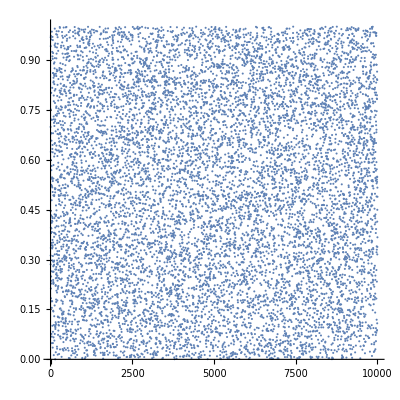
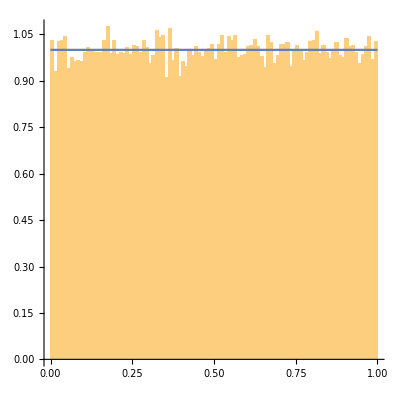
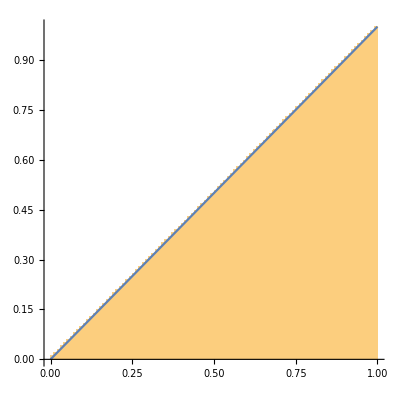
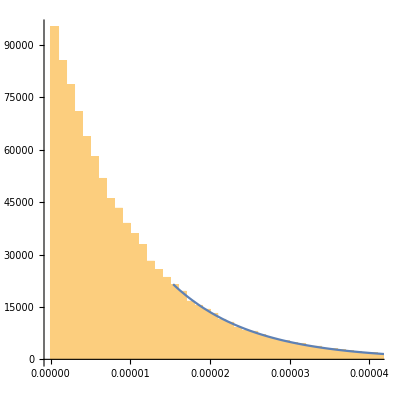
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  | 0.7835946906492
0.79600243383983157 | 0.1675
0.4337918

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937.tst",Real];
testRNG[xi]
```

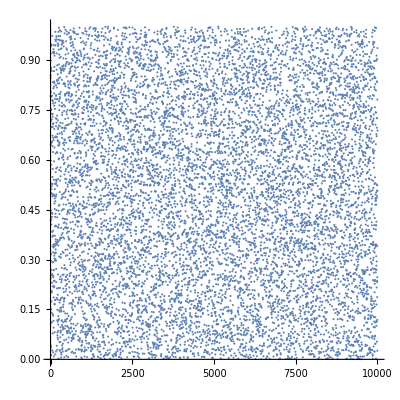
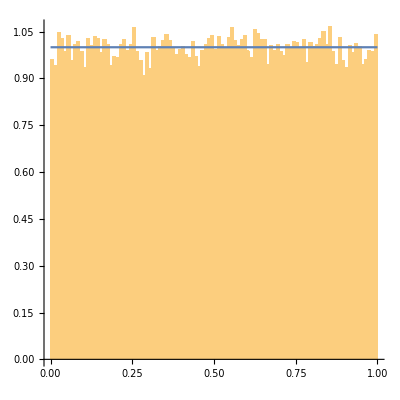
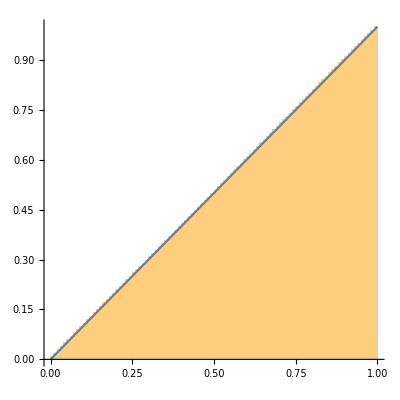
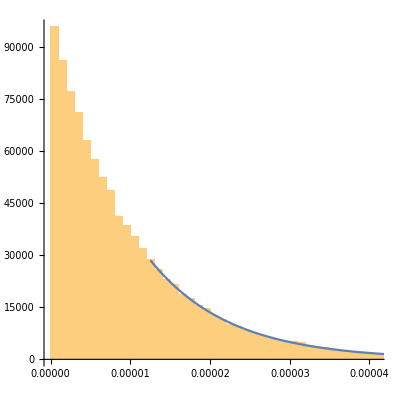
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  | 0.4366698709567
0.55012451334821745 | 0.894
0.5588597

```mathematica
Clear[xi];SetDirectory[NotebookDirectory[]];
xi=ReadList["randoms19937x64.tst",Real];
testRNG[xi]
```